# P1: Equations and Matrices

Numerical Linear Algebra underlies almost every technical computation: NLA encodes, solves and analyzes equations after linearization.

## Preamble

## Fitting Data with Polynomials

Suppose I have a bunch of points from a function and I want to run a polynomial p through the points!

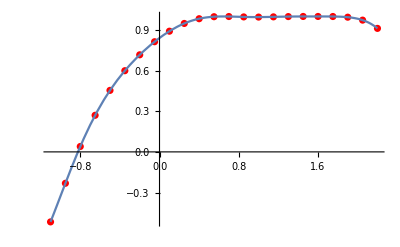

```mathematica
f[x_]:=Sin[x+ Cos[x Sin[x]]]
{a,b}={-1.1,2.2};m=23;
xs=Table[x,{x,a,b,(b-a)/(m-1)}];
fs=Map[f,xs];
Data=Transpose[{xs,fs}];
Show[ListPlot[Data,PlotStyle->Red],Plot[f[x],{x,a,b}]]
```

The polynomial is simply a sum p[x]=c_0+c_1 x+c_2 x^2+… We have m points we should be able to choose m constants to go through the m points. The m equations are 
	c_0 | + | c_1 x_1^1 | + | c_2 x_1^2 | + | … | + | c_(m-1)x_1^(m-1) | = | f(x_1)
c_0 | + | c_1 x_2^1 | + | c_2 x_2^2 | + | … | + | c_(m-1)x_2^(m-1) | = | f(x_2)
  |   |   |   |   |   |   |   |   | ⋮ |  
c_0 | + | c_1 x_m^1 | + | c_2 x_m^2 | + | … | + | c_(m-1)x_m^(m-1) | = | f(x_m)
This is 
	A.c=f
where c={c_0,c_1,…,c_(m-1)}, f={f(x_1),f(x_2),…,f(x_m)}, and A_(i,j)=(x_i)^(j-1).  Lets build them and solve.

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{1.,-1.1,1.21,-1.331,1.4641,-1.61051,1.77156,-1.94872,2.14359,-2.35795,«13»},«9»,«13»} may contain significant numerical errors.

{0.,Null}

0.841471+0.540302 x-0.420741 x^2-0.0900499 x^3-0.234909 x^4+0.424952 x^5+0.222032 x^6-0.205859 x^7-0.143577 x^8-0.0844214 x^9+0.103765 x^10+0.154077 x^11-0.0609431 x^12-0.129994 x^13+0.0688137 x^14+0.0531943 x^15-0.0583393 x^16+0.00987264 x^17+0.0129491 x^18-0.00994152 x^19+0.00330419 x^20-0.000562076 x^21+0.0000398195 x^22

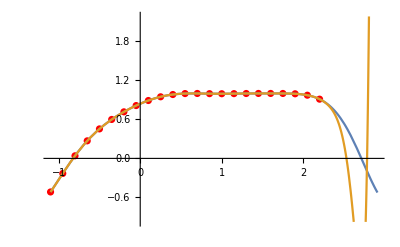

```mathematica
Clear[p]
A=Table[x^(j-1),{x,xs},{j,1,m}]; 
Timing[cs=LinearSolve[A,fs];]
p[x_]=Sum[cs[[j]] x^(j-1),{j,1,m}]
Show[ListPlot[Data,PlotStyle->Red],Plot[{f[x],p[x]},{x,a,b+0.71}],
PlotRange->All]
```

Q1: Is using m large a good idea?
Q2: How was this computed?
Q3: Does software/algorithm make any difference? 
Q4: What does the warning mean?

## Basics

## Multiplying Matrices and Vectors

Random matrices are easy in Mathematica a dot means matrix-vector and matrix-matrix multiplication

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},n];
A.b
```

{0.324976,1.36393,-0.1109,1.32516,0.462232,1.26839}

You get an error if dimensions do not match!

```mathematica
{m,n}={6,5};
A=RandomReal[{-1,1},{m,n}];
b=RandomReal[{-1,1},m];
A.b
```

Dot::dotsh: Tensors {{0.755237,0.0122259,0.0802055,0.367484,-0.866338},«4»,{-0.91344,-0.13125,-0.0499608,0.266026,0.330003}} and {-0.34136,-0.534835,0.952813,0.899603,-0.0543709,-0.342239} have incompatible shapes.

{{0.755237,0.0122259,0.0802055,0.367484,-0.866338},{-0.77251,0.787137,0.0835531,0.315843,0.374011},{-0.252729,0.931303,-0.905584,0.993349,-0.891628},{0.540543,0.27787,0.617256,-0.31858,-0.784536},{-0.785977,0.263449,0.48699,0.838624,-0.186857},{-0.91344,-0.13125,-0.0499608,0.266026,0.330003}}.{-0.34136,-0.534835,0.952813,0.899603,-0.0543709,-0.342239}

It works the same for matrix-matrix multiplication

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Dimensions[A.B]
```

{6,12}

## Multiplying Matrices from scratch: Efficiency!

If C=A.B the C_(i,j)=∑_k A_(i,k)B_(k,j). Defining this yourself is slower (in every way you can imagine) than the built in command!

```mathematica
{m,r,n}={6,5,12};
A=RandomReal[{-1,1},{m,r}];
B=RandomReal[{-1,1},{r,n}];
CBuiltIn=A.B;
CFormula1=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,r}],
{i,m},{j,n}];
Norm[CBuiltIn-CFormula1]
```

5.16129×10^-16

If C=A.B then C=(c_1 | | | c_2 | | | …) where c_j=A.b_j you can implement this.  It will also be slower than the built in matrix multiplication.

```mathematica
{m,n,r}={6,5,12};
A=RandomReal[{-1,1},{m,r}];
B=RandomReal[{-1,1},{r,n}];
CBuiltIn=A.B;
CFormula2=Table[
A.B⟦All,j⟧,
{j,n}]ᵀ;
Norm[CBuiltIn-CFormula2]
```

4.36613×10^-16

We can (and should) race and compare all our versions!

```mathematica
{m,r,n}={12,23,45};
A=RandomReal[{-1,1},{m,r}];
B=RandomReal[{-1,1},{r,n}];
Timing[CBuiltIn=A.B;]
Timing[CFormula1=Table[
Sum[A⟦i,k⟧B⟦k,j⟧,{k,r}],
{i,m},{j,n}];]
Timing[CFormula2=Table[
A.B⟦All,j⟧,
{j,n}]ᵀ;]
```

{0.,Null}

{0.015625,Null}

{0.,Null}

## Block Matrices and Blocks of Matrices

A block matrix 
	A=(A_11 | A_12
A_21 | A_22
A_31 | A_33)
simply slams matrices (of matching dimensions) together.

```mathematica
{m,n}={2,3};
{{A11,A12},
{A21,A22},
{A31,A32}}=RandomReal[{-1,1},{3,2,m,n}];
A=ArrayFlatten[{{A11,A12},{A21,A22},{A31,A32}}];
Dimensions[A];
Map[MatrixForm,{A,A31}]
```

{(-0.754185 | -0.131515 | -0.299865 | 0.667395 | -0.0539802 | -0.182233
-0.500088 | 0.933619 | -0.207412 | -0.567505 | 0.629607 | 0.260204
-0.505866 | -0.658098 | -0.555367 | -0.240305 | 0.331841 | -0.762771
-0.976666 | 0.778946 | 0.108202 | -0.163312 | -0.121132 | -0.0922557
-0.235275 | -0.455498 | 0.856242 | 0.603141 | 0.102037 | 0.758922
-0.495633 | -0.590456 | -0.617362 | -0.935589 | -0.727751 | 0.267957),(-0.235275 | -0.455498 | 0.856242
-0.495633 | -0.590456 | -0.617362)}

You can grab a chunk of a matrix using the range notation

```mathematica
Map[MatrixForm,{A[[1;;m,1;;n]],A11}]
```

{(-0.754185 | -0.131515 | -0.299865
-0.500088 | 0.933619 | -0.207412),(-0.754185 | -0.131515 | -0.299865
-0.500088 | 0.933619 | -0.207412)}

## Inverse Matrices and Linear Solves

Almost all random square matrices A have an inverse A^-1 satisfying A^-1.A=Id

```mathematica
m=23;
A=RandomReal[{-1,1},{m,m}];
AInv=Inverse[A];
Norm[A.AInv-IdentityMatrix[m]]
```

3.3134×10^-13

Most of the time you do not want the inverse! You just want to solve the system A.x=b. It is almost always better (faster and more accurate) to solve the system than compute and apply the inverse.

```mathematica
m=2345;
A=RandomReal[{-1,1},{m,m}]; x=RandomReal[{-1,1},m];
b=A.x;
Timing[AInv=Inverse[A]; xSlow=AInv.b;]
Timing[xFast=LinearSolve[A,b];]
Map[Norm,{xSlow-x,xFast-x}]
```

{0.265625,Null}

{0.140625,Null}

{1.5887×10^-10,1.36627×10^-11}

## Definitions and Theorems

The square matrix V_(i,j)=(x_i)^(j-1) defined by a list x_1,…,x_m is the Vandermonde matrix.

The range (or column space) of a matrix A is the span of columns of A and column rank is its dimension.

The row space of a matrix A is the span of rows of A and row rank is its dimension.

The null space of a matrix A is the set of solutions of A x=0.

A diagonal matrix has zero entries everywhere except on the diagonal.

The m×m identity matrix I_m is the diagonal matrix with 1s on the diagonal.

The inverse A^-1 of an m×m matrix A satisfies A A^-1= A^-1 A=I_m.

Any linear map from L:ℝ^n→ℝ^m is represented A=(L(e_1) | | | L(e_2) | | | … | | | L(e_n))∈ℝ^(m×n).

Theorem 1.3
For A∈ℂ^(m×m) the following are all equivalent: A is invertible; rank(A)=m; range(A)=ℂ^m; null(A)={0}; 0 is not an eigenvalue of A; 0 is not a singular value of A; and det(A)≠0.

## Adjoint and Inner Product

The inner product of two vectors x,y∈ℂ^m is the scalar <x,y>=∑_(i=1)^m OverBar[x_i]y_i

The Euclidean norm of a vector x∈ℂ^m is the scalar ||x||=√(<x,x>)=√(∑_(i=1)^m |x_i|^2)

The angle α between two vectors x,y∈ℝ^m satisfies cos(α)=(<x,y>)/(||x|| ||y||)

The transpose Aᵀ∈ℂ^(n×m) of  A∈ℂ^(m×n) satisfies (Aᵀ)_(i,j)=A_(j,i)

The adjoint of A^*=OverBar[Aᵀ]∈ℂ^(n×m) is the complex conjugate of Aᵀ for A∈ℂ^(m×n).

These definitions make <x,A y> =<A^*x,y>

```mathematica
IP[x_,y_]:=Sum[Conjugate[x⟦i⟧] y⟦i⟧,{i,Length[x]}]
{m,n}={3,4};
A=RandomComplex[{-1-I,1+I},{m,n}];
x=RandomComplex[{-1-I,1+I},m];
y=RandomComplex[{-1-I,1+I},n];
AStar=ConjugateTranspose[A];
{IP[x,A.y],IP[AStar.x,y]}
```

{-1.03755+0.250494 ⅈ,-1.03755+0.250494 ⅈ}

## Orthogonality

Vectors x,y∈ℂ^m are orthogonal if <x,y> =0.

A set of n vectors {x_1,x_2,…,x_n}⊂ℂ^m are orthogonal if <x_i,x_j> =0 for i!=j.

A matrix Q∈ℂ^(m×n) is unitary if Q^*Q=I_n:  Unitary matrix columns q_i are orthogonal with ||q_i||=1.

A matrix Q∈ℝ^(m×n) is orthogonal if QᵀQ=I_n: Orthogonal matrix columns q_i are orthogonal with ||q_i||=1.

Orthogonality gives a simple procedure to split a vector v∈ℂ^m into a piece in the span of the columns of a unitary matrix Q∈ℂ^(m×n) and a residual r∈ℂ^m that is orthogonal to all n columns Q=(q_1 | | | q_2 | | | … | | | q_n).  The recipe is
	r=v-<q_1,v>q_1-<q_2,v>q_2-…-<q_n,v>q_n=v-Q Qᵀ v=(I-QQᵀ)v 
Alternatively we can write
	v=r+∑_(i=1)^n<q_i,v> q_i
and think of the inner products <q_i,v> as a simple recipe for the coefficient of v in each orthogonal direction q_i.

```mathematica
{m,n}={12,4};
Q=Orthogonalize[RandomReal[{-1,1},{n,m}]]ᵀ;
v=RandomReal[{-1,1},m];
r=v-Q.Qᵀ.v
j=1;
r.Q⟦All,j⟧
```

{-0.288071,0.663366,-0.31064,0.560183,-0.312672,-0.178724,0.587947,-0.685884,0.255519,0.432617,0.359529,-0.46472}

-4.16334×10^-17

## Vector Norms

The Euclidean norm ||x(||)_2=√(∑_(i=1)^m |x_i|^2) is the default norm for x∈ℂ^n. However, there are other functions x∈ℂ^m→d(x)∈ℝ which measure distance in the sense that d(x)≥0 for x!=0; d(x+y)≥d(x)+d(y); and d(α x)=|α| d(x).  The most important of these are the p-norms for 1≤p<∞
	||x(||)_p=(∑_(i=1)^m |x_i|^p)^(1/p)
and the limit as p→∞
	||x(||)_∞=max_(1≤i≤m) |x_i|
Every piece of software has a norm function. The default will be the Euclidean two norm.

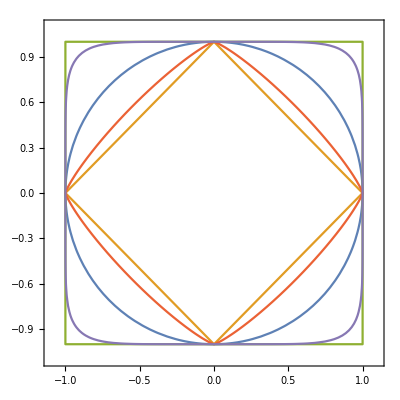

```mathematica
ContourPlot[{
Norm[{x1,x2}]==1,
Norm[{x1,x2},1]==1,
Norm[{x1,x2},∞]==1,
Norm[{x1,x2},1.2]==1,
Norm[{x1,x2},7.2]==1
},{x1,-1.1,1.1},{x2,-1.1,1.1},
Exclusions->None]
```

Rotational invariance is useful.  The Euclidean norm p=2 is the only rotationally invariant vector p-norm. The equivalent 3D pictures are pretty.

```mathematica
ContourPlot3D[{
Norm[{x1,x2,x3}]==1,
Norm[{x1,x2,x3},1]==1,
Norm[{x1,x2,x3},∞]==1,
Norm[{x1,x2,x3},1.2]==1
},{x1,0,1.1},{x2,0,1.1},{x3,0,1.1}]
```

There are other possible distance functions.  For instance, here is a family of exotic vector norms in 3D.

```mathematica
DropSmallNorm[x_,p_]:=Norm[Sort[Abs[x]]⟦2;;-1⟧,p] 
ContourPlot3D[{
DropSmallNorm[{x1,x2,x3},2]==1,
DropSmallNorm[{x1,x2,x3},1]==1
},{x1,0,1.1},{x2,0,1.1},{x3,0,1.1}]
```

## Matrix Norms

Every piece of software computes matrix norms.  There are a lot of possibilities. There is no standard default!

Any function A∈ℂ^(m×n)→d(A)∈ℝ which satisfies d(A)≥0 for A!=0; d(A+B)≥d(A)+d(B); and d(α A)=|α| d(A) is a suitable distance function or norm for matrices.

### Frobenius Norm

The Frobenius norm of A∈ℂ^(m×n) is simply
	||A(||)_F=(∑_(i=1)^m ∑_(j=1)^n|a_(i,j)|^2)^(1/2)
It is unitarily invariant.

### Induced Norms

A matrix norm d(A) is orthogonally invariant if 
	d(Q_1 A Q_2)=d(A) 
for square, conforming, orthogonal matrices Q_1 and Q_2.

The matrix norm for A∈ℂ^(m×n) induced by a vector norm ||x(||)_(n) on the input space ℂ^n and a vector norm ||y(||)_(m) on the output space ℂ^m is
	||A(||)_(m,n)=max_(x∈ℂ^n
x!=0) (||A x(||)_(m))/(||x(||)_(n))=max_(||x(||)_(n)=1) ||A x(||)_(m) 
The most important of these are those induced by the 1,2,∞ vector p norms. Not surprisingly, only the norm induced by the Euclidean (p=2) norm for the input and output spaces is orthogonally invariant.

### SVD based Norms

The Singular Value Decomposition (SVD) of an m×n matrix is A=U Σ Vᵀ where U and V are unitary and Σ is a diagonal m×n matrix with non-increasing, positive diagonal entries.    The singular values of A are the non-diagonal entries of Σ.  Any vector norm of the vector if singular values is a unitarily invariant matrix norm!

The Schatten p-norm of A is just the p-norm of the vector of singular values.

The spectral or operator norm of A is the ∞ norm of the singular values.  So
	||A(||)_op=σ_1
where σ_1 is the largest singular value.

The nuclear norm of A is the 1 norm of the singular values.  So
	||A(||)_*=σ_1+σ_2+…+σ_r=∑_(i=1)^r σ_i
since the r=min(m,n) singular values are positive.

The Ky-Fan k-norm of A just keeps the largest k-singular values (with k≤min(m,n)) in the nuclear norm 
	||A(||)_(KF(k))=∑_(i=1)^k σ_i

The Ky-Fan-Schatten p-k-norm
	(∑_(i=1)^k σ_i^p)^(1/p)
does not have a standard notation.

It turns out that the 2 norm of the singular values is just the Frobenius norm that we met before
	||A(||)_F=(∑_(i=1)^r σ_i^2)^(1/2)

```mathematica
{m,n}={3,4};
RandomReal[{-1,1},{m,n}];
σs=SingularValueList[A];
{Norm[A,"Frobenius"],Norm[σs]}
```

{2.75593,2.75593}

### Induced Norm Visualization

We are going to get some practice with understanding induced norms.

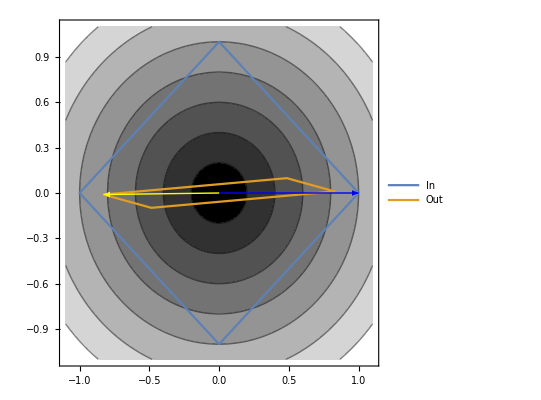

```mathematica
r[θ_,p_]:={Sign[Cos[θ]] Abs[Cos[θ]]^(2/p),Sign[Sin[θ]]*Abs[Sin[θ]]^(2/p)}
θMax[A_,{pIn_,pOut_}]:=ArgMax[Norm[A.r[θ,pIn],pOut],θ]

{pIn, pOut}={1,2};
A=RandomReal[{-1,1},{2,2}];
θStar=θMax[A,{pIn,pOut}];
rStar=r[θStar,pIn];
R=1.1*Max[Abs[A.rStar],1];
Show[
ContourPlot[ Norm[{x1,x2},pOut],{x1,-R,R},{x2,-R,R},
ColorFunction->GrayLevel,Exclusions->None],
ParametricPlot[{r[θ,pIn],A.r[θ,pIn]},{θ,-0.0001, 2π},
ColorFunctionScaling->True,PlotLegends->{"In","Out"},Exclusions->None],
Epilog->{{Blue,Arrow[{{0,0},rStar}]},{Yellow,Arrow[{{0,0},A.rStar}]}}
]
```

Most software implements the special cases of the induced norms (1-1, ∞-∞, 2-2) and the Frobenius norm which have formulas. For Mathematica he default is the “2” norm.

```mathematica
{m,n}={12,34};
A=RandomReal[{-1,1},{m,n}];
TableForm[Table[{t,Norm[A,t]},{t,{"Frobenius",1,2,∞}}]]
```

Frobenius | 11.0972
1 | 7.89241
2 | 4.79607
∞ | 18.0769

### Vector Inequalities

Holder Inequality |<x,y>|≤|x|_p|y|_q where 1/p+1/q=1 e.g.  {p,q}={3,3/2} or {2,2} or {1,∞}.
Cauchy Schwarz Inequality |<x,y>|≤|x|_2|y|_2.

```mathematica
m=12;
{x,y}=RandomReal[{-1,1},{2,m}];
{p,q}={3,3/2};
{1/p+1/q==1,Abs[x.y]≤Norm[x,p]Norm[y,q]}
```

{True,True}

### Product Inequalities

The outer product u⊗v=u v^* is defined by (u⊗v)x=u (v.x) for all x.  It is in ℂ^(m×n) if u∈ℂ^m and v∈ℂ^n.  There is a simple recipe (u⊗v)_ij=u_i v_j

Since ||(u⊗v)x(||)_2=||u (v.x)(||)_2=||u(||)_2|v.x|≤||u(||)_2||v(||)_2||x(||)_2 we have that ||u⊗v(||)_2≤||u(||)_2||v(||)_2. Take x=u to see that ||u⊗v(||)_2=||u(||)_2||v(||)_2.

```mathematica
{m,n}={4,3};
u=RandomInteger[{-9,9},m];
v=RandomInteger[{-9,9},n];
P=KroneckerProduct[u,v];
MatrixForm[P];
{Norm[P],Norm[u]Norm[v]}
```

{12 √82,12 √82}

Rearranging the “parenthesis”  gives product inequalities  for induced matrix norms
	||(AB)x(||)_p_1=||A(B x)(||)_p_1<=||A(||)_(p_1 p_2)||B x(||)_p_2≤||A(||)_(p_1 p_2)||B(||)_(p_2 p_3)||x(||)_p_3
So ||A B(||)_(p_1 p_3)≤||A(||)_(p_1 p_2)||B(||)_(p_2 p_3).   In particular
	||A B(||)_t≤||A(||)_t||B(||)_t
for t=1,2,and ∞. This also holds for the Frobenius norm.

```mathematica
{m,n,r}={3,4,5};
A=RandomReal[{-1,1},{m,n}];
B=RandomReal[{-1,1},{n,r}];
Table[Norm[A.B,t]≤Norm[A,t]*Norm[B,t],{t,{1,2,∞,"Frobenius"}}]
```

{True,True,True,True}

### Unitary/Orthogonal Invariance

A function f on ℂ^(m×n) is unitary invariant if f(Q_1 A Q_2)=f(A) for all square, conforming, unitary matrices Q_1 and Q_2.

A function f on ℝ^(m×n) is orthogonally invariant if f(Q_1 A Q_2)=f(A) for all square, conforming, orthogonal matrices Q_1 and Q_2.

||A(||)_F and ||A(||)_2 i.e. the Frobenius and Operator (induced by the Euclidean 2 norm)norms are unitary and rotationally invariant while ||A(||)_1 and ||A(||)_∞ are not.

```mathematica
{m,n}={12,13};
A=RandomReal[{-1,1},{m,n}];
Q1=Orthogonalize[RandomReal[{-1,1},{m,m}]];
Q2=Orthogonalize[RandomReal[{-1,1},{n,n}]];
TableForm[Table[{t,Norm[A,t],Norm[Q1.A.Q2,t]},{t,{1,2,∞,"Frobenius"}}]]
```

1 | 8.241 | 6.15175
2 | 3.47727 | 3.47727
∞ | 7.3706 | 7.61454
Frobenius | 6.94769 | 6.94769

Any norm defined from the singular values of a matrix is invariant!

## Singular Value Decomposition (SVD)

### Pictures

#### Pictures: ℝ^(2×2)

For any A∈ℝ^(2×2) the image of the unit circle is an ellipse!  The directions and lengths of the axes are clearly of interest!

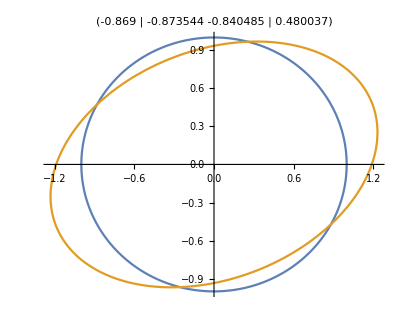

```mathematica
m=2;
A=RandomReal[{-1,1},{m,m}];
ParametricPlot[{{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
PlotLabel->A]
```

#### Pictures: ℝ^(3×3)

For any A∈ℝ^(3×3) the image of the unit sphere is an ellipsoid!  The directions and lengths of the axes are clearly of interest!

```mathematica
m=3;
A=RandomReal[{-1,1},{m,m}];
ParametricPlot3D[{
{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All]
```

-Graphics3D-

#### Pictures: ℝ^(3×2)

For any A∈ℝ^(3×2) the image of the unit circle is an ellipse in 3D!  The directions and lengths of the axes are clearly of interest!

```mathematica
{m,n}={3,2};
A=RandomReal[{-1,1},{m,n}];
ParametricPlot3D[{
A.{Cos[θ],Sin[θ]}
},{θ,0,2π},PlotRange->All,
PlotLabel->A]
```

-Graphics3D-

#### Pictures: ℝ^(2×3)

For any A∈ℝ^(2×3) the image of the unit sphere is an ellipse!  The directions and lengths of the axes are clearly of interest!  The ellipse is covered more than once but it is an ellipse.

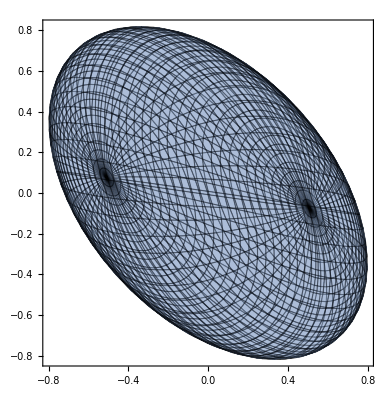

```mathematica
{m,n}={2,3};
A=RandomReal[{-1,1},{m,n}];

ParametricPlot[{
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All]
```

### SVD: Geometric Interpretation

#### SVD: ℝ^(2×2)

The SVD gives us the axes directions and lengths. The column vectors in U are the directions of the axes and the diagonal entries of the diagonal matrix S are the matching lengths.

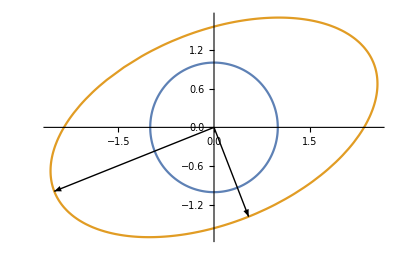

```mathematica
m=2;A=RandomReal[{-2,2},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2}=Uᵀ;{σ1,σ2}=Diagonal[S];
ParametricPlot[{{Cos[θ],Sin[θ]},A.{Cos[θ],Sin[θ]}},{θ,0,2π},PlotRange->All,
Epilog->{{Arrow[{{0,0},σ1 u1}], Arrow[{{0,0},σ2 u2}]}}
]
```

#### SVD: ℝ^(3×3)

The SVD gives us the axes directions and lengths. The column vectors in U are the directions of the axes and the diagonal entries of the diagonal matrix S are the matching lengths.

```mathematica
m=3;A=RandomReal[{-1,1},{m,m}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2,u3}=Uᵀ;{σ1,σ2,σ3}=Diagonal[S];
Show[
ParametricPlot3D[A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]},
{θ,0,2π},{ϕ,0,π},PlotRange->All,
PlotStyle->Opacity[0.2]
],
Graphics3D[{Red,Arrow[{{0,0,0},σ1 u1}], 
Arrow[{{0,0,0},σ2 u2}],
Arrow[{{0,0,0},σ3 u3}]}]]
```

-Graphics3D-

#### SVD: ℝ^(3×2)

For any A∈ℝ^(3×2) the image of the unit circle is an ellipse in 3D!  The SVD gives the info

```mathematica
{m,n}={3,2};A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2,u3}=Uᵀ;
{σ1,σ2}=Diagonal[S];
Show[
ParametricPlot3D[{
A.{Cos[θ],Sin[θ]}
},{θ,0,2π},PlotRange->All],
Graphics3D[{Red,Arrow[{{0,0,0},σ1 u1}], 
Arrow[{{0,0,0},σ2 u2}],
Green,Arrow[{{0,0,0},u3}]}]]
```

-Graphics3D-

#### SVD: ℝ^(2×3)

For any A∈ℝ^(2×3) the image of the unit sphere is an ellipse!  The directions and lengths of the axes are clearly of interest!  The ellipse is covered more than once but it is an ellipse.

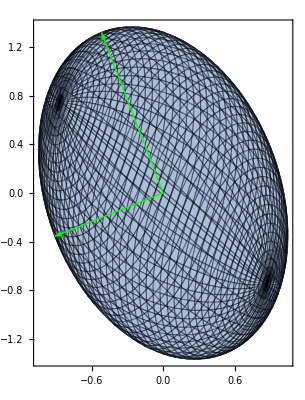

```mathematica
{m,n}={2,3};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
{u1,u2}=Uᵀ;
{σ1,σ2}=Diagonal[S];
ParametricPlot[{
A.{Cos[θ]Sin[ϕ],Sin[θ]Sin[ϕ],Cos[ϕ]}
},{θ,0,2π},{ϕ,0,π},PlotRange->All,
Mesh->All,
Epilog->{Green,Arrow[{{0,0},σ1 u1}],Arrow[{{0,0},σ2 u2}]}
]
```

### SVD: Algebraic Interpretation

I do not know how to draw pictures in general dimensions!

Algebraically the SVD of A∈ℝ^(m×n) gives 
	A=U.S.Vᵀ
where the columns u_k of the m×m matrix U form an orthogonal basis for the output space ℝ^m and the diagonal of the m×n diagonal matrix S gives axis lengths σ_k of the output m-dimensional hyper-ellipse.  The columns of the n×n orthogonal matrix V  give the input vectors v_k that match u_k in the sense that 
	σ_k u_k=A.v_k
The singular values σ_k (the non-negative diagonals of S) are ordered
	σ_1≥σ_2≥…

```mathematica
τ
```

```mathematica
{m,n}={4,5};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A];
Map[Norm,{A-U.S.Vᵀ,Uᵀ.U-IdentityMatrix[m],Vᵀ.V-IdentityMatrix[n]}]
MatrixForm[S]
```

{8.5945×10^-16,6.7537×10^-16,7.09635×10^-16}

(1.89764 | 0. | 0. | 0. | 0.
0. | 1.27487 | 0. | 0. | 0.
0. | 0. | 0.578605 | 0. | 0.
0. | 0. | 0. | 0.504714 | 0.)

### SVD: Thick vs Thin aka Full vs Reduced

A thin SVD drops zero rows and/or columns from the center scaling matrix S and drops the corresponding columns from U and V. In practice, you frequently tell software how many singular values you want (say r) and the software gives you the pieces matching the r biggest singular values!  You now have A≈U.S.Vᵀ but now U and V  are Tall-Skinny matrices. Of course, the columns of U and V are still orthogonal. 

Caution: By default some software gives thin SVDs while some gives thick SVDs.

```mathematica
{m,n,r}={140,100,6};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A,r];
Map[Dimensions,{A,U,S,V}];
Map[Norm,{Uᵀ.U-IdentityMatrix[r],Vᵀ.V-IdentityMatrix[r]}]
Norm[A]
```

{1.3339×10^-15,1.27343×10^-15}

12.193

### Rotationally Invariant Matrix Norms from SVD: A=U.S.Vᵀ

If ||A||=||Q_1.A.Q_2|| for all rotations then 
	||A||=||U.S.Vᵀ||=||Uᵀ.U.S.Vᵀ.V||=||S||
So if σ_r>0 and σ_(r+1)=0 then r is the rank of A and 
	||A(||)_F^2=∑_(i=1)^r σ_i^2
and ||A(||)_2=σ_1. Any rotationally invariant matrix norm is determined by the singular values.  There are Schatten and Ky-Fan norms (this is what I would call a Schatten “p” Ky-Fan “k” norm)
	||σ⟦1;;k⟧(||)_p=(∑_(i=1)^k σ_i^p)^(1/p).
These are sufficiently unusual that they do not have a standard notation.  One special case (the Nuclear Norm) does
	||A(||)_*=∑_(i=1)^r σ_i
It is widely used as a proxy for rank!

## SVD: Interpretation

We can pretend any matrix is diagonal!  All we have to do is use the correct basis for the input and output spaces.

The thick SVD gives us complete information on the matrix!

The rank r of A is the number of non-zero singular values.

The range of A is the span of u_1,u_2,…,u_r and the null space of A is the span of v_(r+1),v_(r+2),…,v_n

||A(||)_2=σ_1 and ||A(||)_F^2=σ_1^2+σ_2^2+…+σ_r^2

The non-zero singular values of A are the square roots of the non-zero eigenvalues of A^*.A or A.A^*

If A=A^* then singular values are the absolute values of the eigenvalues.

```mathematica
{m,n,r}={14,10,3};
A=RandomReal[{-1,1},{m,n}];
{U,S,V}=SingularValueDecomposition[A,r];
Map[Dimensions,{A,U,S,V}]
Map[Norm,{Uᵀ.U-IdentityMatrix[r],Vᵀ.V-IdentityMatrix[r]}]
```

{{14,10},{14,3},{3,3},{10,3}}

{9.40466×10^-16,9.36142×10^-16}

### SVD: Optimal Low Rank Approximation

A thin SVD for a rank r matrix A gives a low rank approximation for A
	A≈A_(μ)=∑_(k=1)^μ σ_k u_k⊗v_k=∑_(k=1)^μ σ_k u_k.v_k^*
In fact, A_(μ) is the best low rank approximation in two senses
	A_(μ) | = | argmin_(rank(B)≤μ) ||A-B(||)_2
A_(μ) | = | argmin_(rank(B)≤μ) ||A-B(||)_F
with ||A-A_(μ)(||)_2=σ_(μ+1) and ||A-A_(μ)(||)_F^2=∑_(k=μ+1)^r σ_k^2.

The proof is easy! Since both norms are unchanged by left or right multiplication by unitary matrices. We can consider the diagonal matrix S=Uᵀ.A.V where A=U.S.Vᵀ is the SVD of A.  The result is pretty clear for diagonal matrices with ordered diagonals.

### SVD: Decomposition and Synthesis

```mathematica
{m,n,r}={12,8,3};
R= RandomReal[{-1,1},{m,r}];
T= RandomReal[{-1,1},{n,r}];
W= RandomReal[{-1,1},{r,r}];
A=R.W.Tᵀ;
{UF,SF,VF}=SingularValueDecomposition[A];
{UR,SR,VR}=SingularValueDecomposition[A,r];
MatrixForm[SR]
MatrixForm[SF]
```

(5.83711 | 0. | 0.
0. | 1.59425 | 0.
0. | 0. | 0.194342)

(5.83711 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.59425 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0.194342 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

### Eigenvalue Decomposition (EVD) and Synthesis

Everyone should know that eigenvalues λ and eigenvectors v satisfy 
	A v = λ v.
Most (but not all) square matrices A∈ℂ^(m×m) have a complete set of m linearly independent eigenvectors which can be  assembled columns  X=(v_1 | | | v_2 | | | … | | | v_m) satisfying A=X.Λ.X^-1 where Λ is the diagonal matrix with the eigenvalues on the diagonal.

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
{λ,X}=Eigensystem[A];X=Xᵀ;
Norm[A-X.DiagonalMatrix[λ].Inverse[X]]
```

1.73099×10^-14

If A is Hermitian A=A^*=OverBar[(Aᵀ)] then you can chose a unitary eigenvector matrix U i.e. 
	A=U.Λ.U^*
If A is real symmetric A=Aᵀ then everything is real and you can chose an orthogonal eigenvector matrix Q i.e. 
	A=Q.Λ.U^ᵀ

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];A=A+Aᵀ;
{λ,Q}=Eigensystem[A];Q=Qᵀ;
Norm[A-Q.DiagonalMatrix[λ].Qᵀ]
```

1.20873×10^-14

You can make matrices with specifc eigenvalues!

```mathematica
λ={1,2,7};
m=Length[λ];
Q=Orthogonalize[RandomReal[{-1,1},{m,m}]];
MatrixForm[A=Q.DiagonalMatrix[λ].Qᵀ]
Eigenvalues[A]
```

(6.63975 | -0.223924 | -1.27895
-0.223924 | 1.16074 | 0.422407
-1.27895 | 0.422407 | 2.1995)

{7.,2.,1.}

## SVD vs (Eigen Value Decomposition)EVD

Existence

Every rectangular or square matrix has an SVD A=U Σ Vᵀ

Most square matrices have an EVD A=X Λ X^-1

Real vs Complex

A real matrix has a real SVD A=U Σ Vᵀ

Most non-symmetric A≠Aᵀ real matrices have complex eigenvalues and eigenvectors.

The second half of our course is going to be about computing SVDs and EVDs.